## Laserpointer wurde gefunden

```mathematica
imgOne=-Graphics-;
blobsOne=-Graphics-;
imgTwo=-Graphics-;
blobsTwo=-Graphics-;
xySimpleOne = ImageValuePositions[blobsOne,White]//Mean
xySimpleTwo = ImageValuePositions[blobsTwo,White]//Mean
```

{350.136,237.682}

{346.833,224.833}

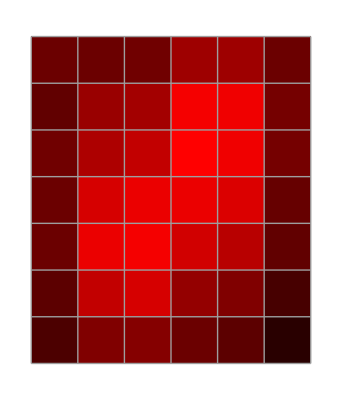
Gefundene Blobs | im Differenzbild | Interpolierte Koordinaten
-Graphics- | -Graphics- | {350.136,237.682}

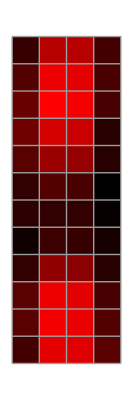
Gefundene Blobs | im Differenzbild | Interpolierte Koordinaten
-Graphics- | -Graphics- | {346.833,224.833}

```mathematica
Print[Grid[{
{"Gefundene Blobs","im Differenzbild", "Interpolierte Koordinaten"},{
ArrayPlot[ImageData[blobsOne][[240;;246,348;;353]], 
Mesh->True,ColorRules->{0->Black,1->White}],
ArrayPlot[ImageData[imgOne][[240;;246,348;;353]], 
Mesh->True,ColorFunction->RGBColor], 
xySimpleOne 
}},Frame->All]];

Print[Grid[{
{"Gefundene Blobs","im Differenzbild", "Interpolierte Koordinaten"},{
ArrayPlot[ImageData[blobsTwo][[250;;261,346;;349]], 
Mesh->True,ColorRules->{0->Black,1->White}],
ArrayPlot[ImageData[imgTwo][[250;;261,346;;349]], 
Mesh->True,ColorFunction->RGBColor],
xySimpleTwo
}},Frame->All]];
```